## Dark Energy Potential

October 29, 2020

#### Starobinsky Potential Approximation from Planck paper Table 5,

→ V(ϕ)=(1-e^-ϕ)^2

#### Yuan’s Dark Energy Potential w/ parameters,

→ V(ϕ)=7/(48(0.005))(e^(-2 ϕ/7.637626158259733)-2 e^(-ϕ/7.637626158259733)+1.1905508 e^((-2ϕ)/(3(7.637626158259733))))

h=1/(√2)
L=-h^2u''(ϕ)+V(ϕ)u(ϕ)
  =-h^2(d^2 u(ϕ))/dϕ^2+V(ϕ)u(ϕ)

#### where u(ϕ) is the wave function for the scalar field of the dark energy potential.

#### Yuan’s plots for her dark energy potential,

```mathematica
h=1/√2;V[x_]:=7/(48(.005)) (ⅇ^(-2x/7.637626158259733)-2 ⅇ^(-x/7.637626158259733)+1.1905508 ⅇ^(-2/3 x/7.637626158259733))
ℒ=-h^2*u''[x]+V[x]*u[x];{vals,funs}=NDEigensystem[ℒ,u[x],{x,-30,30},1,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{MaxCellMeasure->0.01}}}}];
```

```mathematica
vals
```

{0.200339}

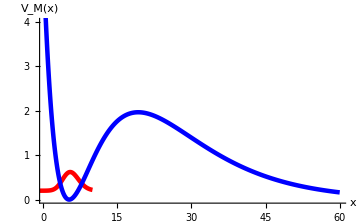

```mathematica
Show[Plot[Evaluate[h*funs+vals],{x,-10,10},BaseStyle->{FontWeight->"Bold", FontSize ->12}, AxesLabel->{"x","V_M(x)"},PlotPoints->1000,  PlotStyle->{Red,Thickness[.009]}],Plot[V[x],{x,.5,60},BaseStyle->{FontWeight->"Bold", FontSize ->12}, AxesLabel->{"x","V_(x)"},PlotPoints->1000,  PlotStyle->{Blue,Thickness[.009]}],PlotRange->{{.5,60},{0,4}},AxesOrigin->{-5,0},ImageSize->Medium]
```

#### Now I’m going to vary the value of lambda (third term coefficient) and get it closer to 0,

```mathematica
Clear[L,V]
```

```mathematica
h=1/√2;
V[ϕ_]:=7/(48(.005)) (ⅇ^(-2ϕ/7.637626158259733)-2 ⅇ^(-ϕ/7.637626158259733)+0.8 ⅇ^(-2/3 ϕ/7.637626158259733))
ℒ=-h^2*u''[ϕ]+V[ϕ]*u[ϕ];{vals,funs}=NDEigensystem[ℒ,u[ϕ],{ϕ,-30,30},1,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{MaxCellMeasure->0.01}}}}];
```

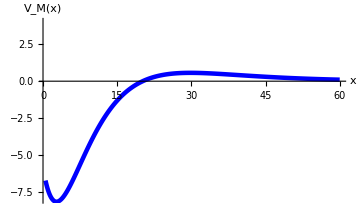

```mathematica
Show[Plot[Evaluate[h*funs+vals],{x,-10,10},BaseStyle->{FontWeight->"Bold", FontSize ->12}, AxesLabel->{"x","V_M(x)"},PlotPoints->1000,  PlotStyle->{Red,Thickness[.009]}],Plot[V[x],{x,.5,60},BaseStyle->{FontWeight->"Bold", FontSize ->12}, AxesLabel->{"x","V_(x)"},PlotPoints->1000,  PlotStyle->{Blue,Thickness[.009]}],PlotRange->{{.5,60},{-8,4}},ImageSize->Medium]
```

#### For lambda = 0.2,

```mathematica
Clear[L,V]
```

```mathematica
h=1/√2;
V[ϕ_]:=7/(48(.005)) (ⅇ^(-2ϕ/7.637626158259733)-2 ⅇ^(-ϕ/7.637626158259733)+0.2 ⅇ^(-2/3 ϕ/7.637626158259733))
ℒ=-h^2*u''[ϕ]+V[ϕ]*u[ϕ];{vals,funs}=NDEigensystem[ℒ,u[ϕ],{ϕ,-30,30},1,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{MaxCellMeasure->0.01}}}}];
```

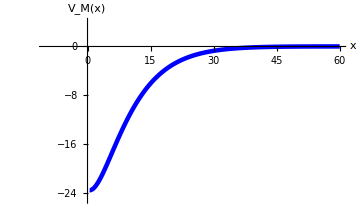

```mathematica
Show[Plot[Evaluate[h*funs+vals],{x,-10,10},BaseStyle->{FontWeight->"Bold", FontSize ->12}, AxesLabel->{"x","V_M(x)"},PlotPoints->1000,  PlotStyle->{Red,Thickness[.009]}],Plot[V[x],{x,.5,60},BaseStyle->{FontWeight->"Bold", FontSize ->12}, AxesLabel->{"x","V_(x)"},PlotPoints->1000,  PlotStyle->{Blue,Thickness[.009]}],PlotRange->{{-10,60},{-25,4}},ImageSize->Medium]
```

#### Below I made the coefficient of the dark energy term (lambda) into a variable and made a Manipulate Plot,

```mathematica
Clear[L,V]
h=1/Sqrt[2];

V[x_,lambda_]:=7/(48 (.005)) (E^(-2 x/7.637626158259733)-2 E^(-x/7.637626158259733)+lambda*E^(-2/3 x/7.637626158259733))

L[lambda_]:=-h^2*u''[x]+V[x,lambda]*u[x]

f[lambda_]:=NDEigensystem[L[lambda],u[x],{x,-30,30},1,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{MaxCellMeasure->0.01}}}}]

Manipulate[{funs,vals}=f[lambda];
Show[Plot[h*funs+vals,{x,-10,10},AxesLabel->{"x","V(x)"},PlotStyle->Red,PlotPoints->1000],Plot[V[x,lambda],{x,0.5,60},PlotStyle->Blue,PlotPoints->1000],PlotRange->{{0,60},{-25,10}}],{lambda,0.1,2}]
```

#### Below is an animation of the same plot of varying lambda from 0.1 to 2,

```mathematica
Animate[Show[Plot[h*funs+vals,{x,-10,10},AxesLabel->{"x","V(x)"},PlotStyle->Red,PlotPoints->1000],Plot[V[x,lambda],{x,0.5,60},PlotStyle->Blue,PlotPoints->1000],PlotRange->{{0,60},{-25,10}}],{lambda,0.1,2},AnimationRunning->False]
```

```mathematica
Clear[L,V]
```

```mathematica
h=1/√2;
V[ϕ_]:=7/(48(.005)) (ⅇ^(-2ϕ/7.637626158259733)-2 ⅇ^(-ϕ/7.637626158259733)+10^-6 ⅇ^(-2/3 ϕ/7.637626158259733))
ℒ=-h^2*u''[ϕ]+V[ϕ]*u[ϕ];{vals,funs}=NDEigensystem[ℒ,u[ϕ],{ϕ,-30,30},1,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{MaxCellMeasure->0.01}}}}];
```

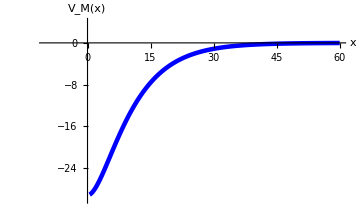

```mathematica
Show[Plot[Evaluate[h*funs+vals],{x,-10,10},BaseStyle->{FontWeight->"Bold", FontSize ->12}, AxesLabel->{"x","V_M(x)"},PlotPoints->1000,  PlotStyle->{Red,Thickness[.009]}],Plot[V[x],{x,.5,60},BaseStyle->{FontWeight->"Bold", FontSize ->12}, AxesLabel->{"x","V_(x)"},PlotPoints->1000,  PlotStyle->{Blue,Thickness[.009]}],PlotRange->{{-10,60},{-30,4}},ImageSize->Medium]
```